# Statistical Analysis for WaterGate

101 years of annual peak flow data (in cf/s, or cubic feet per second) for the Rio Grande at Embudo, New Mexico.

```mathematica
PeakFlow = {5890, 6270,8790,6860,5300,5160,3110,8980,4700,1690,5600,7400,2500,16200,14000,2080,7190,7330,8560,8600,3580,7280,12700,14400,7500,4820,8780,1580,5500,9500,5240,5850,2240,1740,7180,4340,832,5900,3630,6690,5440,2410,1990,12000,10800,2220,8770,5380,1950,4080,10200,9990,1470,710,8720,2000,1860,2200,1020,5000,6840,2760,2320,2340,3980,966,952,5200,1950,3550,3270,3140,2250,1860,1090,6620,1050,3700,2290,2480,1490,9000,5080,2930,5010,5660,6010,8420,7500,9280,1110,2540,2480,5730,3330,5580,7410,936,4930,2530,3310} ;
```

ListLinePlot of the values

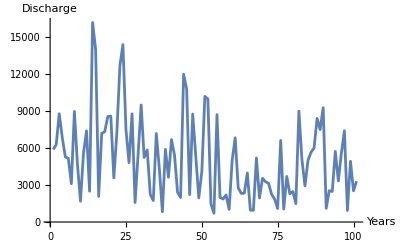

```mathematica
ListLinePlot[PeakFlow, AxesLabel->{"Years", "Discharge"}]
```

Histogram depicting the values. We can see that the histogram is very clearly skewed towards the right, and therefore we can attempt to correct this

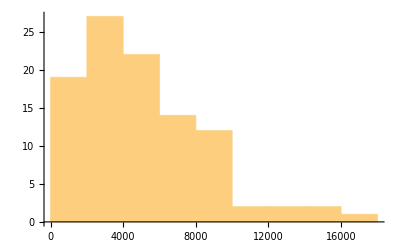

```mathematica
PeakFlowHistogram = Histogram[PeakFlow]
```

Applying Log to each value makes the table more balanced.

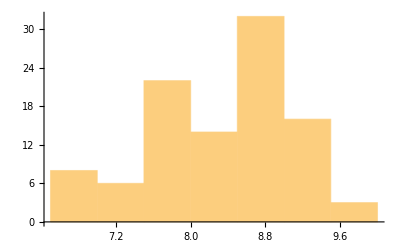

```mathematica
Histogram[Log[PeakFlow]]
```

```mathematica
meanval = Mean[Log[PeakFlow]];
```

```mathematica
dev = StandardDeviation[Log[PeakFlow]];
```

```mathematica
Plot[PDF[LogNormalDistribution[meanval,dev], x], {x,0,17000}, PlotStyle->Thickness[0.008], DisplayFunction->Identity]
```

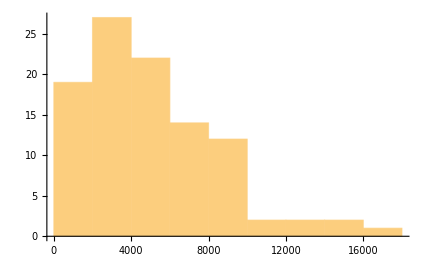
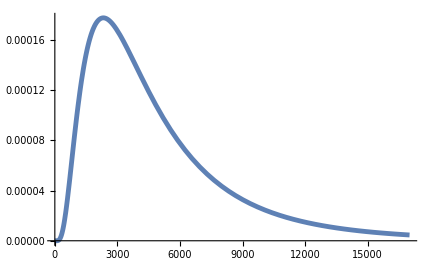

```mathematica
List[PeakFlowHistogram,%574]
```

We can see an obvious correlation between the histogram and the probability density function  - the LogNormalDistribution which is created by taking the mean values and the standard deviation.

Now, time for more statistical analysis  - We can assign values for our next probability density function - ExtremeValueDistribution which uses the values of α and β.

```mathematica
β = N@StandardDeviation[PeakFlow]Sqrt[6]/Pi
```

2599.56

```mathematica
α = N@Mean[PeakFlow] - 0.5772%
```

3574.54

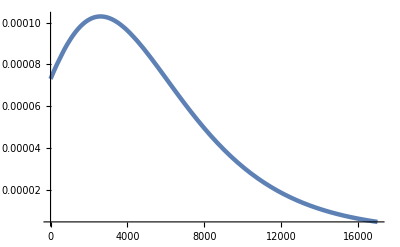

```mathematica
Plot[PDF[ExtremeValueDistribution[2599.5617596256748,3574.542853334159],x], {x,0,17000}, PlotRange->All, PlotStyle->Thickness[0.008], DisplayFunction->Identity]
```

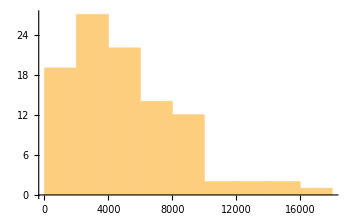
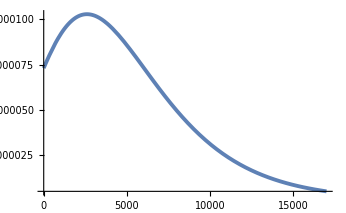

```mathematica
List[PeakFlowHistogram, %606]
```

```mathematica
RankedFlow =Sort[PeakFlow]
```

{710,832,936,952,966,1020,1050,1090,1110,1470,1490,1580,1690,1740,1860,1860,1950,1950,1990,2000,2080,2200,2220,2240,2250,2290,2320,2340,2410,2480,2480,2500,2530,2540,2760,2930,3110,3140,3270,3310,3330,3550,3580,3630,3700,3980,4080,4340,4700,4820,4930,5000,5010,5080,5160,5200,5240,5300,5380,5440,5500,5580,5600,5660,5730,5850,5890,5900,6010,6270,6620,6690,6840,6860,7180,7190,7280,7330,7400,7410,7500,7500,8420,8560,8600,8720,8770,8780,8790,8980,9000,9280,9500,9990,10200,10800,12000,12700,14000,14400,16200}

```mathematica
n = Length[PeakFlow]
```

101

```mathematica
Print[α]
```

3574.54

Next, we can look at a Cumulative Distribution Function (ExtremeValueDistribution) using the values of α and β.

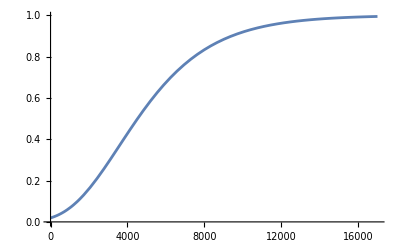

```mathematica
FrequencyPlot2 = Plot[CDF[ExtremeValueDistribution[α,β], x], {x,0,17000}]
```

We also look at another CDF, this time - it’s the LogNormalDistribution function which uses the mean values and the standard deviation

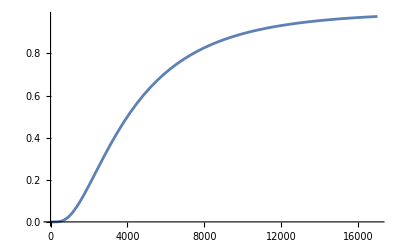

```mathematica
FrequencyPlot3 = Plot[CDF[LogNormalDistribution[meanval,dev], x], {x,0,17000}]
```

And finally, we can show the intersection of the two probability density functions

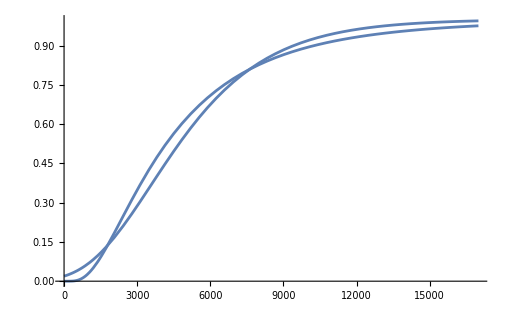

```mathematica
Show[FrequencyPlot2, FrequencyPlot3]
```

```mathematica
levels=Select[Drop[ExampleData[{"Statistics","LakeMeadLevels"}],None,1]//Flatten,Positive];
```

```mathematica
maxLevel=1229;
```

```mathematica
relativeLevels=levels/maxLevel;
```

```mathematica
edist=EstimatedDistribution[relativeLevels,KumaraswamyDistribution[α,β]]
```

KumaraswamyDistribution[30.543,2.7868]

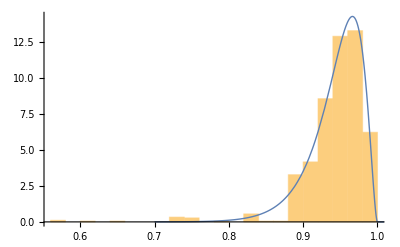

```mathematica
Show[Histogram[relativeLevels,Automatic,"PDF"],Plot[PDF[edist,x],{x,0.7,1.1},PlotStyle->Thick]]
```

```mathematica
drought=1125;
```

```mathematica
N[Probability[x*maxLevel<drought,x\[Distributed]edist]];
```

```mathematica
maxLevel Mean[edist]
```

1160.59

```mathematica
maxLevel Mean[edist]
```

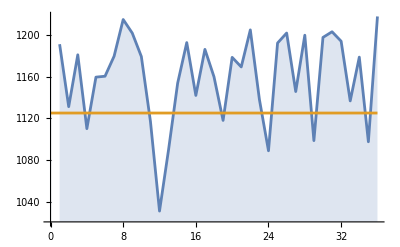

```mathematica
ListPlot[{maxLevel RandomVariate[edist,36],{{0,drought},{36,drought}}},Filling->{1->Axis},Joined->{True,True}]
```

```mathematica
;
```

```mathematica
ToExpression/@%
```

```mathematica
;
```

```mathematica
ToExpression/@%
```

```mathematica
edistBeta2=EstimatedDistribution[divideSequence,BetaDistribution[α,β], MaxIterations->Infinity]
```

BetaDistribution[13020.3,8.84502]

```mathematica
Show[Histogram[divideSequence,Automatic,"PDF", AxesLabel->Automatic],Plot[PDF[%496,x],{x,0.9988, 1},PlotStyle->AbsoluteThickness]]
```

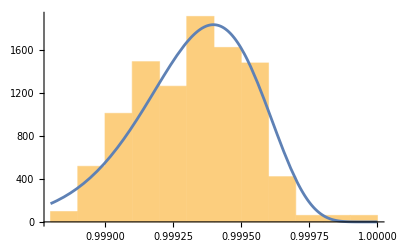

```mathematica
edistGamma=EstimatedDistribution[divideSequence,GammaDistribution[α,β], MaxIterations->Infinity]
```

GammaDistribution[2.41922×10^7,4.13077×10^-8]

```mathematica
Show[Histogram[divideSequence,Automatic,"PDF", AxesLabel->Automatic],Plot[PDF[edistGamma,x],{x,0.9988, 1},PlotStyle->AbsoluteThickness] ]
```

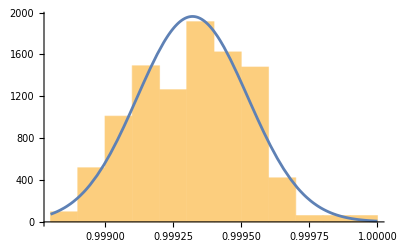

```mathematica
edistBeta=EstimatedDistribution[divideSequence,BetaDistribution[α,β], MaxIterations->Infinity]
```

BetaDistribution[13020.3,8.84502]

```mathematica
Show[Histogram[divideSequence,Automatic,"PDF", AxesLabel->Automatic],Plot[PDF[edistBeta,x],{x,0.9988, 1},PlotStyle->AbsoluteThickness] ]
```

-Graphics-

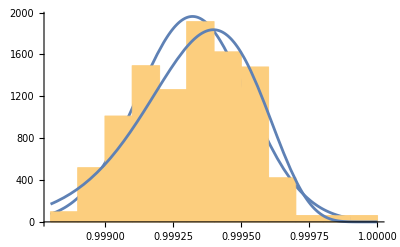

```mathematica
Show[%443, %445]
```

```mathematica
levels=Select[Drop[ExampleData[{"Statistics","LakeMeadLevels"}],None,1]//Flatten,Positive];
```

```mathematica
maxLevel = 1229;
```

```mathematica
relativeLevels = levels/maxLevel;
```

```mathematica
edist=EstimatedDistribution[relativeLevels,KumaraswamyDistribution[α,β]]
```

KumaraswamyDistribution[30.543,2.7868]

```mathematica
KumaraswamyDistribution[30.54299350888491,2.7867956521488817]
```

```mathematica
Show[Histogram[relativeLevels,Automatic,"PDF"],Plot[PDF[edist,x],{x,0.7,1.1},PlotStyle->Thick]]
```

-Graphics-